# Newton’s Method Review

## Initialization Cells

```mathematica
SetOptions[MatrixPlot,ColorRules->{0.0->LightGreen},Mesh->All];
```

## Derivatives

For x:ℝ→ℝ^n  
	x'(t)=lim_(h->0) (x(t+h)-x(t))/h 
and x':ℝ→ℝ^n. The same definition makes sense for A:ℝ→ℝ^(n×n) and A':ℝ→ℝ^(n×n). Second and higher derivatives (written x''(t) and x'''(t) etc.) are defined by applying the definition repeatedly

For f:ℝ^n→ℝ^m we have ∂_j f(x)=lim_(h→0) (f(x+h e_j)-f(x))/h where e_j∈ℝ^nis the vector with a 1 in the j^thslot and zeros everywhere else and ∂_j f:ℝ^n→ℝ^m.  It is common to write ∂_j f=(∂f)/(∂x_j). If  
	f(x)=(f_1(x)
f_2(x)
⋮
f_m(x)) 
then the gradient  ∇f:ℝ^n→ℝ^(m×n)  or Jacobian matrix J(x)=∇f(x) is
	J(x)=∇f(x)=(∂_1 f(x) | | | ∂_2 f(x) | | | … | | | ∂_n f(x))∈ℝ^(m×n).
The Jacobian has entries 	
	(J(x))_(i,j)=(f_i(x))/(∂x_j).

A smooth function has as many derivatives as we need.

```mathematica
f[{x1_,x2_}]:= {x1, x2, x1+x2}
Dimensions[D[f[{x1,x2}],{{x1,x2}}]]
```

{3,2}

## Taylor/Maclaurin/Power Series

For smooth f:ℝ→ℝ^n the power series  
	f(t)~∑_(i=0)^∞ (f^(i)(0))/(i!)t^i 
matches derivatives of all orders f^(0)(0)=f(0), f^(1)(0)=f'(0), f^(2)(0)=f''(0), … at t=0.  Functions are frequently defined (inside some radius of convergence) by a power series.  For instance, in Calculus II i.e. n=1 we learned that
	e^t | = | ∑_(i=0)^∞ t^i/(i!) | for|t|<∞
sin(t) | = | ∑_(i=0)^∞ (-1)^i t^(2i+1)/((2i+1)!) | for|t|<∞
cos(t) | = | ∑_(i=0)^∞ (-1)^i t^(2i)/((2i)!) | for|t|<∞
log(1+t) | = | ∑_(i=1)^∞ (-1)^i t^i/i | for|t|<1

```mathematica
Series[Log[1+t],{t,0,12}]
```

t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+O[t]^13

For smooth f:ℝ→ℝ^n the power series  
	f(t)~∑_(i=0)^∞ (f^(i)(0))/(i!)t^i 
matches derivatives of all orders f^(0)(0)=f(0), f^(1)(0)=f'(0), f^(2)(0)=f''(0), … at t=0.  Functions are frequently defined (inside some radius of convergence) by a power series.  For instance,
	e^t | = | ∑_(i=0)^∞ t^i/(i!) | for|t|<∞
sin(t) | = | ∑_(i=0)^∞ (-1)^i t^(2i+1)/((2i+1)!) | for|t|<∞
cos(t) | = | ∑_(i=0)^∞ (-1)^i t^(2i)/((2i)!) | for|t|<∞
log(1+t) | = | ∑_(i=1)^∞ (-1)^i t^i/i | for|t|<1

Power series are much more complicated for f:ℝ^m→ℝ^n because the structure of higher derivatives is more complicated: Df:ℝ^m→ℝ^(n×m) and DDf:ℝ^m→ℝ^(n×m×m).  In words: f is a vector represented by the components f_i; Df is a matrix represented by the components ∂f_i/∂x_j; DDf is a tensor represented by the components ∂^2 f_i/∂x_j∂x_k.

## Integration

For smooth f:ℝ→ℝ^n the integral can be defined by the limit of the right hand Riemann sum 
	∫_a^b f(t)dt=lim_(n->∞) ∑_(i=1)^n f(a+i h)h
on a uniform grid with h=(b-a)/n.  For smooth functions right hand sums, left hand sums, midpoint sums 
	RHS(n) | = | ∑_(i=1)^n f(a+i h)h                
LHS(n) | = | ∑_(i=0)^(n-1) f(a+i h)h                
MP(n) | = | ∑_(i=0)^(n-1) f(a+(i+0.5) h)h
all have the same limit as n->∞ and h=(b-a)/n->0. The Trapezoid rule and Simpson’s rule
	Trap(n) | = | (LHS(n)+RHS(n))/2
Simp(n) | = | (LHS(n)+4MP(n)+RHS(n))/6  
converge much faster than the simpler rules.

## Fundamental Theorem of Calculus (FTC)

Integration and differentiation are inverse process. Calculus books typically present several different versions.

A: For smooth F:ℝ→ℝ^n if 
	∫_a^b F'(τ)dτ=F(b)-F(a).

B: For smooth f:ℝ→ℝ^n if
	F(t)=∫_a^t f(τ)dτ 
then F'(t)=f(t).

C: For smooth f:ℝ→ℝ^n if
	F'(t)=f(t) 
then F(t)=∫_a^t f(τ)dτ+F(a).  The constant F(a) is called a constant of integration. Constants of integration are the "+C" you were taught to stick on the back of indefinite integrals.

## Inverse Function Theorem

A smooth function f:ℝ^n→ℝ^n is invertible near x_0∈ℝ if J(x_0) is an invertible matrix.

#### 1D Example

We should make sure we understand this example.

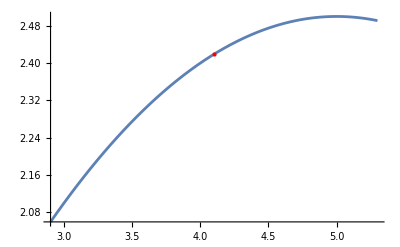

```mathematica
Clear[f,J,x1,x2]
f[x1_]:=x1-0.1 x1^2
J[x1_]=D[f[x1],x1];
ϵ=1.2;
x10=4.1;
J0=J[x10];
Plot[f[x1],{x1, x10-ϵ,x10+ϵ},
Epilog->{Red,Point[{x10,f[x10]}]}]
```

#### 2D Example

We should make sure we understand this example.

{{1+0.2 x1+Cos[x1+x2],Cos[x1+x2]},{-Sin[x1-x2],1+Sin[x1-x2]}}

{{0.210008,-0.989992},{0.841471,0.158529}}

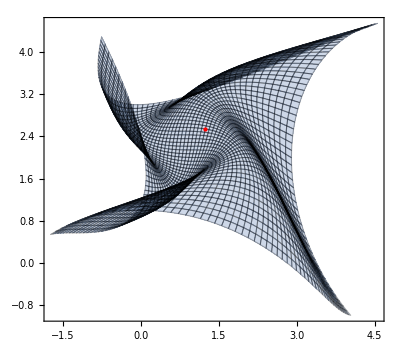

```mathematica
Clear[f,J,x1,x2]
f[{x1_,x2_}]:={x1+0.1 x1^2+ Sin[x1 +x2],x2+Cos[x1-x2]}
J[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}]
ϵ=2;
{x10,x20}={1.0,2.0};
J0=J[{x10,x20}]
ParametricPlot[f[{x1,x2}],{x1, x10-ϵ,x10+ϵ},{x2,x20-ϵ,x20+ϵ},
Mesh->All,
Epilog->{Red,Point[f[{x10,x20}]]}]
```